```mathematica
Clear[LatticeIrrational,latticeRational]
```

```mathematica
LatticeIrrational=Table[{j,0},{j,1,316/2}];
```

```mathematica
latticeRational=Table[{j,0},{j,1,282/2}];
```

```mathematica
largestXRational = 282/2;
largestXIrrational = 316/2;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataEnergyPBC,dataEnergyOBC]
```

```mathematica
dataEnergyPBC=Import["IrrationalSlope/EigenvaluesParent60DislocationIrrational12to14mP100PBC.dat"];
```

```mathematica
dataEnergyOBC=Import["IrrationalSlope/EigenvaluesParent60DislocationIrrational12to14mP100OBC.dat"];
```

Import::nffil: File IrrationalSlope/EigenvaluesParent60DislocationIrrational12to14mP100OBC.dat not found during Import.

```mathematica
dataEnergyPBC;
```

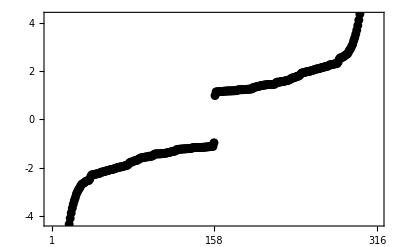

```mathematica
Show[
(** ListPlot[dataEnergyPBC,Frame-> True,Axes-> False,PlotRange-> {{0,2*largestXIrrational},{-4.25,4.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,largestXIrrational,2*largestXIrrational},None}},BaseStyle-> 18], **)

ListPlot[dataEnergyPBC,PlotStyle-> {Black,PointSize[0.016]},
Frame-> True,Axes-> False,PlotRange-> {{0,2*largestXIrrational},{-4.25,4.25}},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,largestXIrrational,2*largestXIrrational},None}},BaseStyle-> 18]
(** ,

ListPlot[{dataEnergyPBC[[largestXIrrational]]},PlotStyle-> {Red,PointSize[0.018]}] **)
(** ,

Plot[-1.5,{x,210,230},PlotStyle-> {Thick,Red}],
Plot[-3.0,{x,210,230},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{260,-1.5}],Inset["PBC",{260,-3.0}]} **)
]
```

```mathematica
dataEnergyPBC[[largestXIrrational]]
```

{158,-0.976552}

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc,colorfuncBW]
```

```mathematica
dataLDoSPBC=Import["IrrationalSlope/LDOSParent60DislocationIrrational12to14mM005PBC.dat"];
```

```mathematica
dataLDoSOBC=Import["BBCDataFiles/mPM1DataFiles/LDOSParent60Irrational6to12mM1OBC.dat"];
```

Import::nffil: File BBCDataFiles/mPM1DataFiles/LDOSParent60Irrational6to12mM1OBC.dat not found during Import.

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@dataLDoSPBC[[All,3]]
```

{0,0.110001}

```mathematica
rng={0,0.22}
```

{0,0.22}

```mathematica
P1=BarLegend[{colorfuncBW[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"1.1"},{rng[[2]]-10^-3,"2.2"}}]
```

```mathematica
(** Crop appropriately and put the numbers in inkscape **)
```

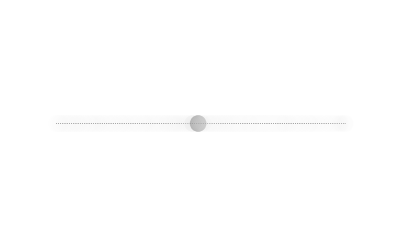

```mathematica
Show[
ListPlot[LatticeIrrational,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-10,Max[Flatten[LatticeIrrational]]+10},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfuncBW[#[[3]],rng[[2]]],Point[#[[1;;2]]]
}&/@dataLDoSPBC,
BaseStyle-> 18
]

]
```